```mathematica
SetOptions[Plot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLinearPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[DiscretePlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];SetOptions[ListLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListLogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[BarChart,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
```

## Generalized Polya urn model

### No reinforcement

```mathematica
kk=500;     (* number of types *)
time=5000;     (* simulation time *)
w0=1;   (* initial value *)
w=Table[w0,{i,1,kk}];    (* # of balls in the urn for each type *)
For[n=0,n<time,n++,r=RandomInteger[{1,kk}];w[[r]]++];
xi=w/Apply[Plus,w];
```

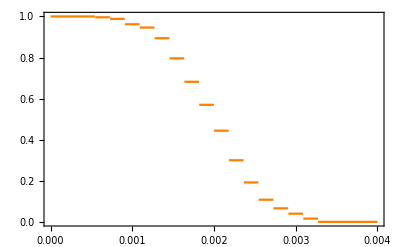

```mathematica
pl1=Plot[1-CDF[EmpiricalDistribution[xi],x],{x,0 ,0.004},PlotStyle->Orange]
```

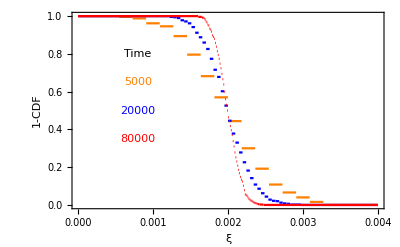

```mathematica
Show[pl1,pl2,pl3,Graphics[{Text["Time",{0.0008,0.8}],Orange,Text["5000",{0.0008,0.65}],Blue,Text["20000",{0.0008,0.5}],Red,Text["80000",{0.0008,0.35}]}],FrameLabel->{"ξ","1-CDF"}]
```

### Linear reinforcement

```mathematica
kk=500;     (* number of types *)
time=5000;     (* simulation time *)
w0=1;   (* initial value *)
w=Table[w0,{i,1,kk}];    (* # of balls in the urn for each type *)
types=Table[i,{i,1,kk}];    (* list of types *)
For[n=0,n<time,n++,r=RandomSample[w->types,1];w[[r]]++];
xi=w/Apply[Plus,w];
```

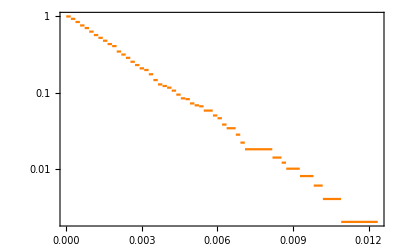

```mathematica
ppl1=LogPlot[1-CDF[EmpiricalDistribution[xi],x],{x,0 ,Max[xi]},PlotStyle->Orange]
```

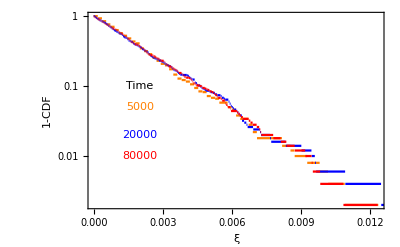

```mathematica
Show[ppl1,ppl2,ppl3,Graphics[{Text["Time",{0.002,Log[0.1]}],Orange,Text["5000",{0.002,Log[0.05]}],Blue,Text["20000",{0.002,Log[0.02]}],Red,Text["80000",{0.002,Log[0.01]}]}],FrameLabel->{"ξ","1-CDF"}]
```

#### Nonlinear reinforcement

```mathematica
kk=500;     (* number of types *)
time=80000;     (* simulation time *)
w0=3;   (* initial value *)
g=1.5;   (* reinforcement parameter *)
w=Table[w0,{i,1,kk}];    (* # of balls in the urn for each type *)
wlist=Table[w0^g,{i,1,kk}];    (* list of weights *)
types=Table[i,{i,1,kk}];    (* list of types *)
For[n=0,n<time,n++,r=RandomSample[wlist->types,1];w[[r]]++;wlist[[r]]=w[[r]]^g];
xi=w/Apply[Plus,w];
```

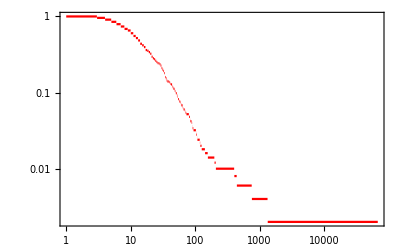

```mathematica
p5=LogLogPlot[1-CDF[EmpiricalDistribution[w],x],{x,1 ,Max[w]},PlotStyle->Red]
```

```mathematica
pp5=LogLogPlot[1-CDF[EmpiricalDistribution[xi],x],{x,Min[xi],Max[xi]},PlotStyle->Red];
```

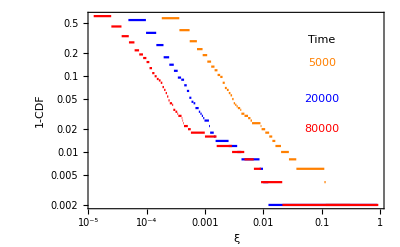

```mathematica
Show[pp1,pp2,pp3,Graphics[{Text["Time",{Log[0.1],Log[0.3]}],Orange,Text["5000",{Log[0.1],Log[0.15]}],Blue,Text["20000",{Log[0.1],Log[0.05]}],Red,Text["80000",{Log[0.1],Log[0.02]}]}],PlotRange->All,FrameLabel->{"ξ","1-CDF"}]
```

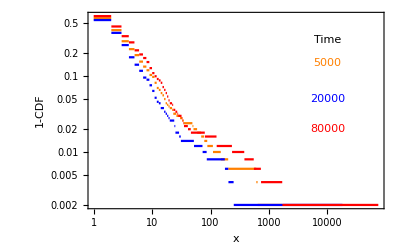

```mathematica
Show[p1,p2,p3,Graphics[{Text["Time",{Log[10000],Log[0.3]}],Orange,Text["5000",{Log[10000],Log[0.15]}],Blue,Text["20000",{Log[10000],Log[0.05]}],Red,Text["80000",{Log[10000],Log[0.02]}]}],PlotRange->All,FrameLabel->{"x","1-CDF"}]
```